```mathematica
Clear["Global`*"]
```

```mathematica
(*Funktionen*)
GiveX[l_,y_]:=Extract[l,Position[l,{xs_,ys_}/;ys==y]][[1,1]]
GiveX[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;ys>=Range[[1]]&&ys<=Range[[2]]]][[1,1]]
GiveY[l_,x_]:=Extract[l,Position[l,{xs_,ys_}/;xs==x]][[1,2]]
GiveY[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;xs>=Range[[1]]&&xs<=Range[[2]]]][[1,2]]
GiveXY[l_,z_]:=Extract[l,Position[l,{xs_,ys_,zs_}/;zs==z]][[1]][[{1,2}]]
FindMaximumList[l_]:={GiveX[l,Max[l]],Max[l]}(*Annahme: y>x*)
CheckEq[l1_List,l2_List,n_]:=Sequence[]
CheckEq[l1_List,l2_List,n_]:=l1[[n]]/;(l1[[n,2]]≥l2[[n,2]]&&l1[[n,2]]≤l2[[n+5,2]])||(l1[[n,2]]≤l2[[n,2]]&&l1[[n,2]]≥l2[[n+5,2]])
CheckEqPoints[l1_List,l2_List,start_:1]:=Flatten[Table[{CheckEq[l1,l2,n]},{n,start,Length[l1]-5}]/.{}->Sequence[],1]
```

```mathematica
(*Parameter*)
M=50.; (*Masse des Gegengewichts*)
m=0.5; (*Masse des Geschosses*)
d=0.1; (*Dicke des Wurfarms*)
Tm=0.;(*Plot und Integrations Range*)
Tp=1.3;
θ0=-Pi/4; (*Startwinkel des Wurfarms, wenn keine Einschränkung aus Geometrie*)
n=2000;(*Anzahl der Auswertungspunkte*)
(*Konstanten*)
g=9.81;
(*Dichte Holz*)
ρ=670.;
```

```mathematica
(*Startwerte*)
L0=3.5; (*Länge des Wurfarms*)
r0=2.86;(*Länge der Schlinge*)
h0=1.0;(*Länge der Aufhängung des Gegengewichts*)
x0=0.4;(*Abstand Aufhängung des Wurfarms zum SP, guter Start: L0/4*)
```

```mathematica
(*abgeleitete Parameter*)
L1[L_,x_]:=L/2-x
L2[L_,x_]:=L/2+x
μ[L_]:=L d^2 ρ
V[L_,x_]:=M g L1[L,x] - m g L2[L,x] - μ[L] g x
i[L_,x_]:=μ[L](1/12 L^2+x^2)+m L2[L,x]^2+M L1[L,x]^2
```

```mathematica
(*abgeleitete Parameter aus den Startwerten*)
L1[L0,x0]
L2[L0,x0]
L1[L0,x0]/L2[L0,x0]
r0/(L1[L0,x0]+L2[L0,x0])
r0/L2[L0,x0]
h0/L1[L0,x0]
```

1.35

2.15

0.627907

0.817143

1.33023

0.740741

```mathematica
(*Einschränkung an den Startwinkel aus Geometrie*)
(*Achtung: θstart muss größer als Pi/4=0.785 sein, sonst wird der optimale Abwurfwinkel nie erreicht*)
(*θstart[L_,h_,x_]:=Re[-ArcCos[(L1[L,x] Sin[Pi/4]+h)/L2[L,x]]HeavisideTheta[L2[L,x]-L1[L,x] Sin[Pi/4]-h]+θ0 HeavisideTheta[L1[L,x] Sin[Pi/4]+h-L2[L,x]]]*)
θstart[L_,h_,x_]:=θ0
θstart[L0,h0,x0]
```

-π/4

```mathematica
(*Lösung der DGL*)
s[L_,r_,h_,x_]:=NDSolve[{i[L,x] θ''[t]==M L1[L,x] h φ''[t]Sin[φ[t]+θ[t]]+M L1[L,x] h φ'[t]^2 Cos[φ[t]+θ[t]]-m L2[L,x] r ψ''[t]Cos[ψ[t]-θ[t]]+m L2[L,x] r ψ'[t]^2 Sin[ψ[t]-θ[t]]+V[L,x] Cos[θ[t]],h φ''[t]==L1[L,x] θ''[t]Sin[φ[t]+θ[t]]+L1[L,x] θ'[t]^2 Cos[φ[t]+θ[t]]-g Sin[φ[t]],r ψ''[t]==-L2[L,x] θ''[t]Cos[ψ[t]-θ[t]]-L2[L,x] θ'[t]^2 Sin[ψ[t]-θ[t]]-g Cos[ψ[t]],θ[0]==θstart[L,h,x],θ'[0]==0,φ[0]==0,φ'[0]==0,ψ[0]==-Pi+0.1,ψ'[0]==0},{θ,φ,ψ},{t,Tm,Tp}]
```

```mathematica
Pv[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[Sqrt[(L2[L,x] θ'[t])^2+(r ψ'[t])^2+2 L2[L,x]ψ'[t]θ'[t]Cos[ψ[t]-θ[t]]]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Geschossgeschwindigkeit",AxesLabel->{"t","v(t)"}]]
Ppsi[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[ψ[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Psi",AxesLabel->{"t","ψ(t)"}]]
Pphi[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[φ[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Phi",AxesLabel->{"t","ψ(t)"}]]
Pth[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[θ[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Theta",AxesLabel->{"t","θ(t)"}]]
```

```mathematica
thList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(θ[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
psiList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(ψ[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
phiList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(φ[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*Betrag der Geschossgeschwindigkeit*)
vList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,Re[(Sqrt[(L2[L,x] θ'[t])^2+(r ψ'[t])^2+2 L2[L,x]ψ'[t]θ'[t]Cos[ψ[t]-θ[t]]]/.S)[[1]]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*x-Komponente der Geschossgeschwindigkeit*)
vxList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(-L2[L,x] Sin[θ[t]] θ'[t]-r Sin[ψ[t]] ψ'[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*y-Komponente der Geschossgeschwindigkeit*)
vyList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(L2[L,x] Cos[θ[t]] θ'[t]+r Cos[ψ[t]] ψ'[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*Integrierte Wurfweite*)
sWurf[vx_,vy_,h_]:=vx(vy+Sqrt[2 g h +vy^2])/g
sWurfList[L_,r_,h_,x_]:=Block[{S,vx,vy,H},
S=s[L,r,h,x];
vx=((-L2[L,x] Sin[θ[t]] θ'[t]-r Sin[ψ[t]] ψ'[t])/.S)[[1]];
vy=((L2[L,x] Cos[θ[t]] θ'[t]+r Cos[ψ[t]] ψ'[t])/.S)[[1]];
H=((L Sin[θ[t]]+h)/.S)[[1]];
Table[{t,Re[sWurf[vx,vy,H]]},{t,Tm,Tp,(Tp-Tm)/n}]]
tmax[L_,r_,h_,x_]:=FindMaximumList[Abs[sWurfList[L,r,h,x]]][[1]]
smax[L_,r_,h_,x_]:=GiveY[sWurfList[L,r,h,x],tmax[L,r,h,x]]
vmax[L_,r_,h_,x_]:=GiveY[vList[L,r,h,x],tmax[L,r,h,x]]
```

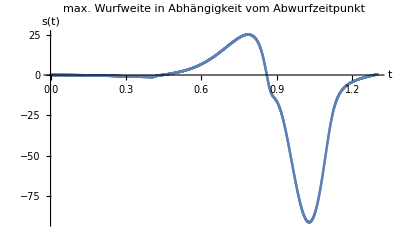

```mathematica
ListPlot[sWurfList[L0,r0,h0,x0],PlotRange->All,PlotLabel->"max. Wurfweite in Abhängigkeit vom Abwurfzeitpunkt",AxesLabel->{"t","s(t)"}]
```

1.0283

-91.3603

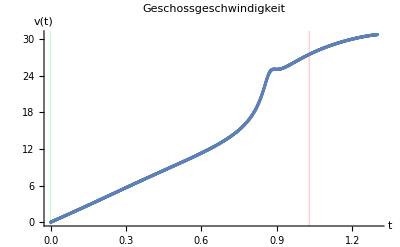

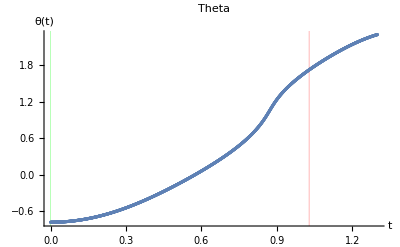

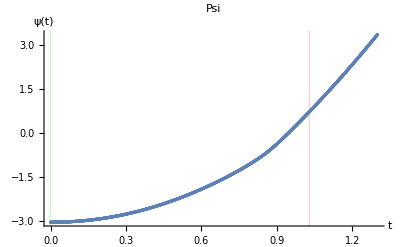

```mathematica
t0=tmax[L0,r0,h0,x0]
s0=smax[L0,r0,h0,x0]
Show[Pv[L0,r0,h0,x0,t0],ListPlot[vList[L0,r0,h0,x0]]]
Show[Pth[L0,r0,h0,x0,t0],ListPlot[thList[L0,r0,h0,x0]]]
Show[Ppsi[L0,r0,h0,x0,t0],ListPlot[psiList[L0,r0,h0,x0]]]
```

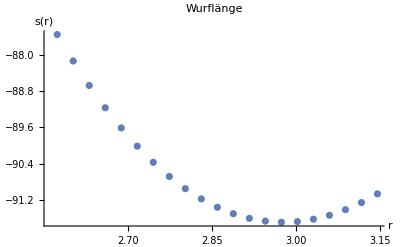

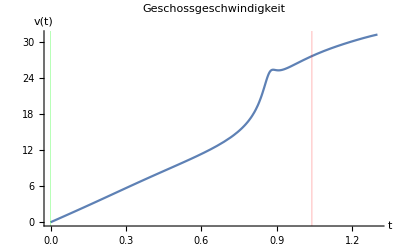

Abwurfzeitpunkt t0 = 1.03935

neuer Startwert für L0 = 3.5

neuer Startwert für r0 = 2.9744

neuer Startwert für h0 = 1.

neuer Startwert für x0 = 0.4

vmax = 27.6247

smax = -91.6904

```mathematica
(*1D Analyse in r*)
smaxr=Table[{r,smax[L0,r,h0,x0]},{r,0.9r0,1.1r0,0.1r0/10}];
ListPlot[smaxr,PlotLabel->"Wurflänge",AxesLabel->{"r","s(r)"}]
rmax=FindMaximumList[Abs[smaxr]][[1]];
r0=rmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
```

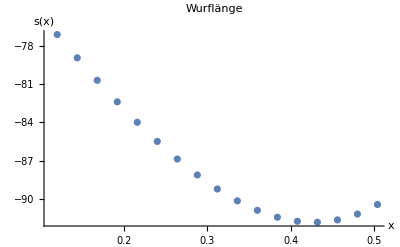

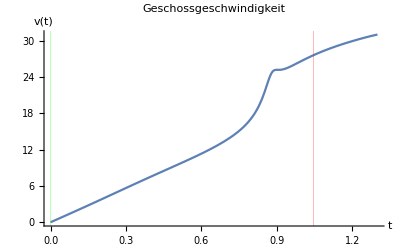

Abwurfzeitpunkt t0 = 1.0452

neuer Startwert für L0 = 3.5

neuer Startwert für r0 = 2.9744

neuer Startwert für h0 = 1.

neuer Startwert für x0 = 0.432

vmax = 27.5762

smax = -91.8473

```mathematica
(*1D Analyse in x*)
smaxx=Table[{x,smax[L0,r0,h0,x]},{x,0.3x0,1.3 x0,0.6x0/10}];
ListPlot[smaxx,PlotLabel->"Wurflänge",AxesLabel->{"x","s(x)"}]
xmax=FindMaximumList[Abs[smaxx]][[1]];
x0=xmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
```

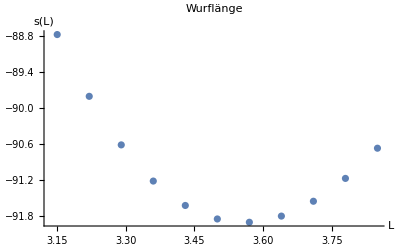

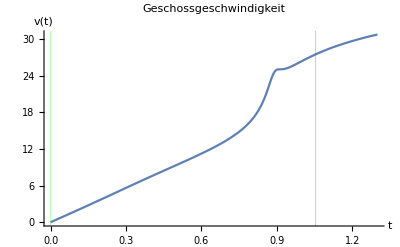

Abwurfzeitpunkt t0 = 1.05365

neuer Startwert für L0 = 3.57

neuer Startwert für r0 = 2.9744

neuer Startwert für h0 = 1.

neuer Startwert für x0 = 0.432

vmax = 27.4916

smax = -91.902

```mathematica
(*1D Analyse in L*)
smaxL=Table[{L,smax[L,r0,h0,x0]},{L,0.9L0,1.1 L0,0.2L0/10}];
ListPlot[smaxL,PlotLabel->"Wurflänge",AxesLabel->{"L","s(L)"}]
Lmax=FindMaximumList[Abs[smaxL]][[1]];
L0=Lmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
```

```mathematica
(*Notiz: Optimierung über h konvergiert nicht. h sollte deshalb so groß wie technisch möglich gewählt werden.*)
(*1D Analyse in h*)
(*smaxh=Table[{h,smax[L0,r0,h,x0]},{h,0.9h0,1.1 h0,0.2h0/10}];
ListPlot[smaxh,PlotLabel->"Wurflänge",AxesLabel->{"h","s(h)"}]
hmax=FindMaximumList[Abs[smaxh]][[1]];
h0=hmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]*)
```

```mathematica
Tend=t0;
(*Vektoren*)
r1List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(L2[L,x]Cos[θ[t]])/.S][[1]],Evaluate[(L2[L,x]Sin[θ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
r2List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(L2[L,x]Cos[θ[t]]+r Cos[ψ[t]])/.S][[1]],Evaluate[(L2[L,x]Sin[θ[t]]+r Sin[ψ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
r3List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(-L1[L,x]Cos[θ[t]])/.S][[1]],Evaluate[(-L1[L,x]Sin[θ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
r4List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(-L1[L,x]Cos[θ[t]]-h Sin[φ[t]])/.S][[1]],Evaluate[(-L1[L,x]Sin[θ[t]]-h Cos[φ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
Manipulate[
Show[ListPlot[{r2List[L0,r0,h0,x0],r1List[L0,r0,h0,x0]},PlotRange->{{-L2[L0,x0]-r0,L2[L0,x0]+r0},{-L2[L0,x0]-r0,L2[L0,x0]+r0}},Frame->True,ImageSize->{600,600},AspectRatio->1],Graphics[Line[{r4List[L0,r0,h0,x0][[Round[n]]],r3List[L0,r0,h0,x0][[Round[n]]],{0,0},r1List[L0,r0,h0,x0][[Round[n]]],r2List[L0,r0,h0,x0][[Round[n]]]}]]],{n,1,Length[r1List[L0,r0,h0,x0]]}]
```